## τα from fitting CRSISF, SISF to stretched exponential

```mathematica
(*saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";*)
```

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.825";
```

```mathematica
p0=3.825
```

3.825

```mathematica
Directory[]
```

/home/chengling

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

```mathematica
nestedArray={{{True,False},{False,True},{True,True}}};
falseIndices=Position[nestedArray,False,{3},Heads->False]
```

{{1,1,2},{1,2,1}}

```mathematica
list[[1,1,1]]
```

23

```mathematica
list={{{23,2},{4,6}},{{25,8},{4,78}},{{26,4185},{4,4}}};
indicesToDelete={{1,1,1}};
result=Delete[list,List/@indicesToDelete]
```

Delete::psl: Position specification {1,1,1} in {{{23,2},{4,6}},{{25,8},{4,78}},{{26,4185},{4,4}}} is not a machine-sized integer or a list of machine-sized integers.

Delete[{{{23,2},{4,6}},{{25,8},{4,78}},{{26,4185},{4,4}}},{{{1,1,1}}}]

## Data reading

```mathematica
saveFolders={"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.825","/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800","/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.750"};
```

```mathematica
p0s={3.825,3.8,3.75}
```

{3.825,3.8,3.75}

```mathematica
temperatures={{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000},{1, 3, 4 ,8 ,15,40 ,70 ,150 ,250, 600 ,2000, 2500 ,4500, 9500},{4 ,5 ,7 ,10 ,30 ,70, 150 ,700,1400, 4000 ,9500}}
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

{{1,2,4,9,15,25,40,60,80,120,200,300,1000,1500,5000,10000},{1,3,4,8,15,40,70,150,250,600,2000,2500,4500,9500},{4,5,7,10,30,70,150,700,1400,4000,9500}}

```mathematica
overlapCRoverlap=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/overlapCRoverlap_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/overlapCRoverlap_N4096_p3.8000_T0.06300000_waitingTime10000_idx14.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/overlapCRoverlap_N4096_p3.8000_T0.06300000_waitingTime10000_idx15.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/overlapCRoverlap_N4096_p3.8000_T0.06300000_waitingTime10000_idx17.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
SISFCRSISF=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/SISFCRSISF_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/SISFCRSISF_N4096_p3.8000_T0.06300000_waitingTime10000_idx14.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/SISFCRSISF_N4096_p3.8000_T0.06300000_waitingTime10000_idx15.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/SISFCRSISF_N4096_p3.8000_T0.06300000_waitingTime10000_idx17.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::format: Cannot import data as Data.

```mathematica
CRoverlapMean=Table[Table[Table[Mean[DeleteCases[Table[overlapCRoverlap[[p,T,i,2,rec]],{i,Length[overlapCRoverlap[[p,T]]]}],_Missing|_Part|0.]],{rec,Max[Table[Length[overlapCRoverlap[[p,T,i,1]]],{i,Length[overlapCRoverlap[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 104 of … does not exist.

Part::partw: Part 105 of … does not exist.

Part::partw: Part 106 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
overlapMean=Table[Table[Table[Mean[DeleteCases[Table[overlapCRoverlap[[p,T,i,1,rec]],{i,Length[overlapCRoverlap[[p,T]]]}],_Missing|_Part|0.]],{rec,Max[Table[Length[overlapCRoverlap[[p,T,i,1]]],{i,Length[overlapCRoverlap[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 104 of … does not exist.

Part::partw: Part 105 of … does not exist.

Part::partw: Part 106 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
CRSISFMean=Table[Table[Table[Mean[DeleteCases[Table[SISFCRSISF[[p,T,i,2,rec]],{i,Length[SISFCRSISF[[p,T]]]}],_Missing|_Part|0.]],{rec,Max[Table[Length[SISFCRSISF[[p,T,i,2]]],{i,Length[SISFCRSISF[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 104 of … does not exist.

Part::partw: Part 105 of … does not exist.

Part::partw: Part 106 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
SISFMean=Table[Table[Table[Mean[DeleteCases[Table[SISFCRSISF[[p,T,i,1,rec]],{i,Length[SISFCRSISF[[p,T]]]}],_Missing|_Part|0.]],{rec,Max[Table[Length[SISFCRSISF[[p,T,i,1]]]-3,{i,Length[SISFCRSISF[[p,T]]]}]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 104 of … does not exist.

Part::partw: Part 105 of … does not exist.

Part::partw: Part 106 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
time={0.,0.00999999999476131,0.01999999998952262,0.02999999998428393,0.03999999997904524,0.04999999997380655,0.05999999996856786,0.06999999996332917,0.07999999995809048,0.0899999999528518,0.0999999999476131,0.10999999994237442,0.12999999993189704,0.13999999992665835,0.15999999991618097,0.1799999999057036,0.1999999998952262,0.21999999988474883,0.24999999986903276,0.2799999998533167,0.31999999983236194,0.34999999981664587,0.3999999997904524,0.449999999764259,0.4999999997380655,0.5599999997066334,0.6299999996699626,0.709999999628053,0.7899999995861435,0.8899999995337566,0.999999999476131,1.1199999994132668,1.2599999993399251,1.4099999992613448,1.579999999172287,1.7799999990675133,1.999999998952262,2.2399999988265336,2.509999998685089,2.8199999985226896,3.159999998344574,3.5499999981402652,3.9799999979150016,4.469999997658306,5.009999997375417,5.6199999970558565,6.309999996694387,7.079999996291008,7.9399999958404806,8.909999995332328,9.99999999476131,11.21999999412219,12.58999999340449,14.129999992597732,15.849999991696677,17.77999999068561,19.949999989548814,22.389999988270574,25.119999986840412,28.179999985237373,31.619999983435264,35.47999998141313,39.80999997914478,44.669999976598774,50.11999997374369,56.22999997054285,63.09999996694387,70.78999996291532,79.42999995838909,89.12999995330756,99.9999999476131,112.1999999412219,125.88999993405014,141.2499999260035,158.489999916972,177.82999990684038,199.52999989547243,223.86999988272146,251.18999986840936,281.8399998523528,316.2299998343369,354.80999981412606,398.10999979144253,446.6799997659982,501.1899997374421,562.3399997054075,630.9599996694596,707.949999629127,794.3299995838752,891.2499995331018,999.999999476131,1122.0199994122086,1258.9299993404857,1412.5399992600142,1584.8899991697253,1778.2799990684143,1995.2599989547452,2238.719998827204,2511.889998684099,2818.3799985235382,3162.2799983433797,3548.129998141245,3981.069997914441,4466.839997659961,5011.869997374437,5623.40999705407,6309.569996694612,7079.459996291291,7943.279995838762,8912.509995331013,9999.99999476131,11220.179994122096,12589.249993404883,14125.379992600152,15848.929991697238,17782.78999068415,19952.619989547442,22387.209988272036,25118.85998684101,28183.829985235367,31622.779984235283,35481.33998782885,39810.7199918609,44668.35999638493,50118.72000146097,56234.13000715639,63095.73001354675,70794.58002071686,79432.82002876185,89125.09003778848,100000.00004791653}
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,3162.28,3548.13,3981.07,4466.84,5011.87,5623.41,6309.57,7079.46,7943.28,8912.51,10000.,11220.2,12589.2,14125.4,15848.9,17782.8,19952.6,22387.2,25118.9,28183.8,31622.8,35481.3,39810.7,44668.4,50118.7,56234.1,63095.7,70794.6,79432.8,89125.1,100000.}

```mathematica
Flatten[Normal[test2[[4]]]]-test2[[4,1,1]]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,-40000.}

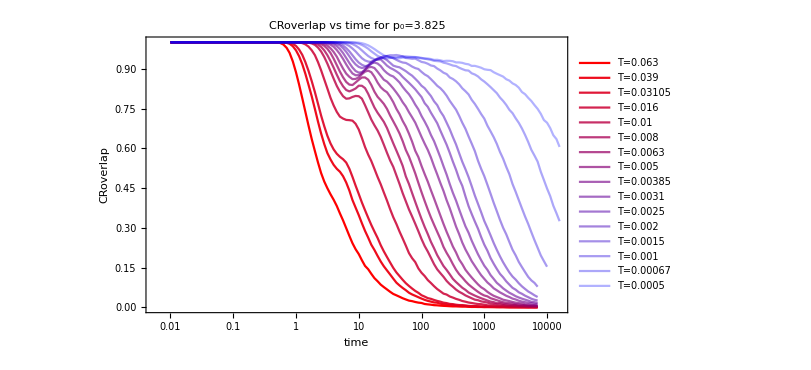
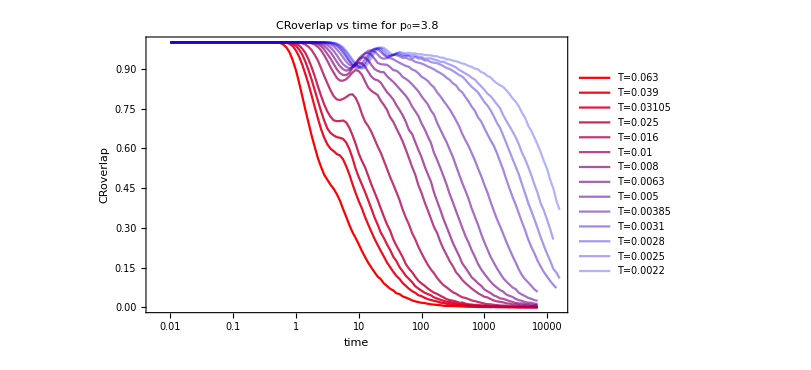
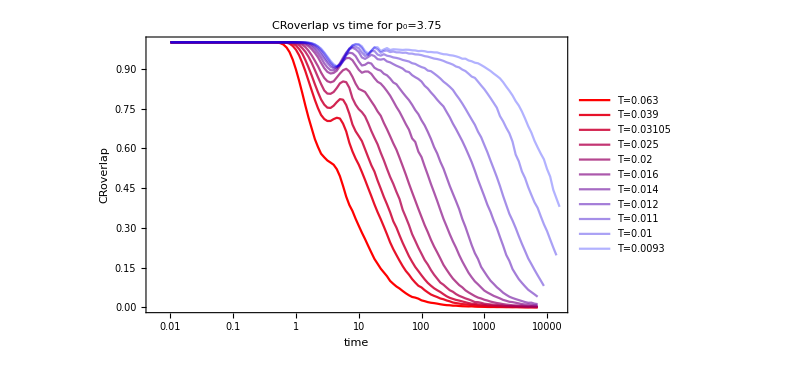

```mathematica
CRoverlapPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],CRoverlapMean[[p,T,rec]]},{rec,Length[CRoverlapMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}];
Column[CRoverlapPlots]
```

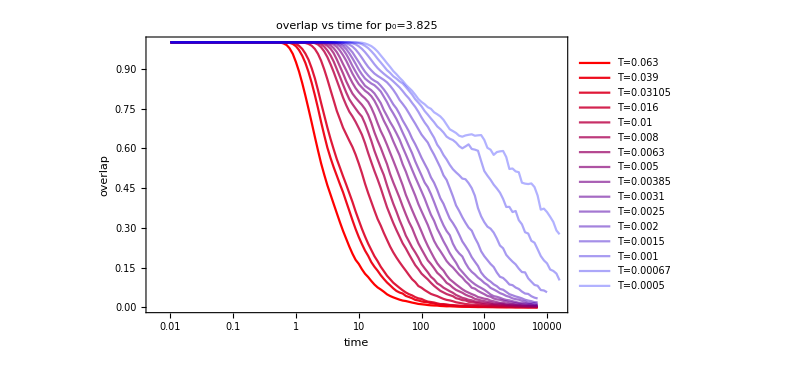
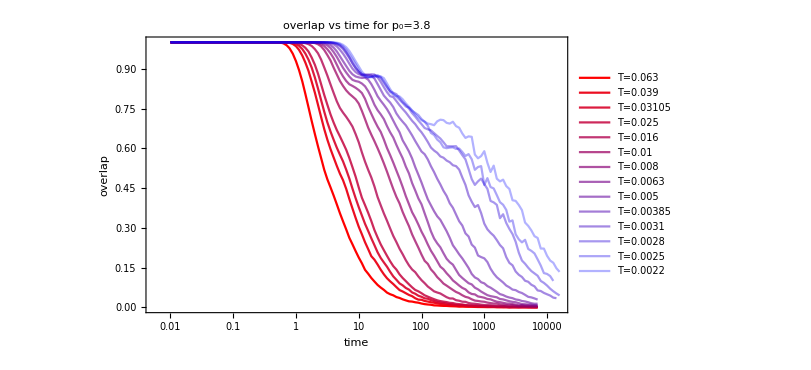
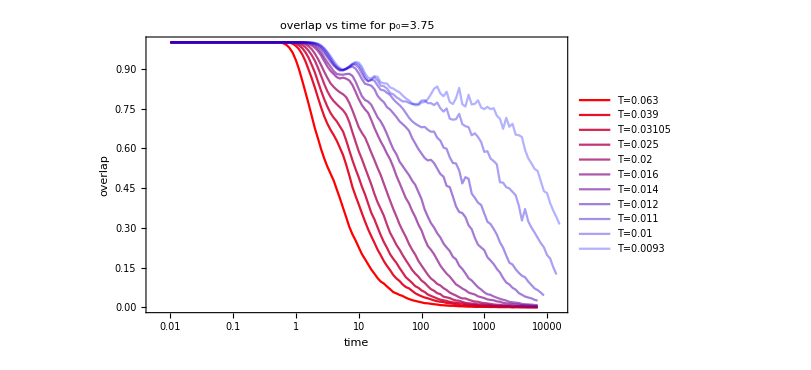

```mathematica
overlapPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],overlapMean[[p,T,rec]]},{rec,Length[overlapMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}];
Column[overlapPlots]
```

```mathematica
overlapCRoverlap[[3,10,1]]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
sisfCRSISF[[3,10,1]]
```

<|/firstValue→NetCDFTools`Private`postProcessDataArray[Real64,$Failed,{96}],/secondValue→NetCDFTools`Private`postProcessDataArray[Real64,$Failed,{96}]|>

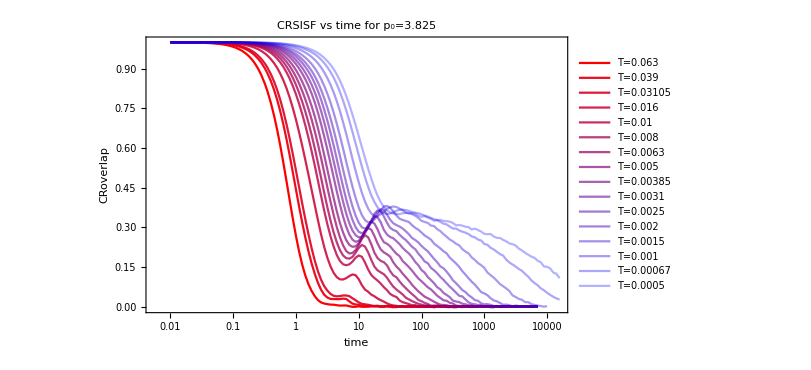
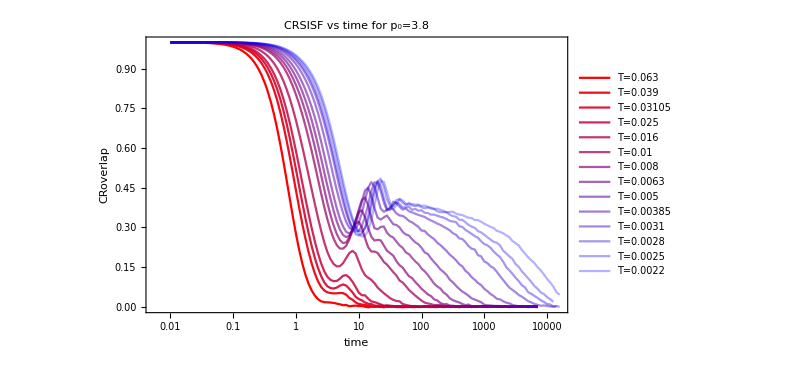
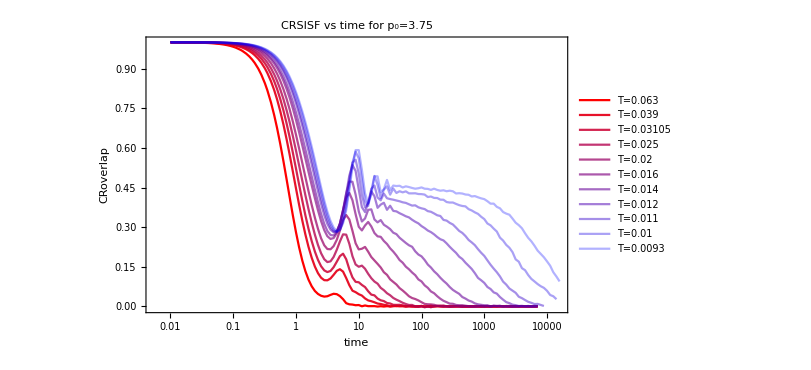

```mathematica
CRSISFPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}];
Column[CRSISFPlots]
```

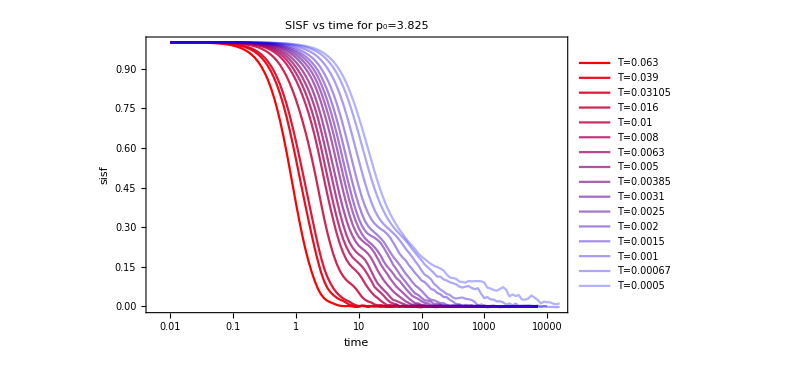
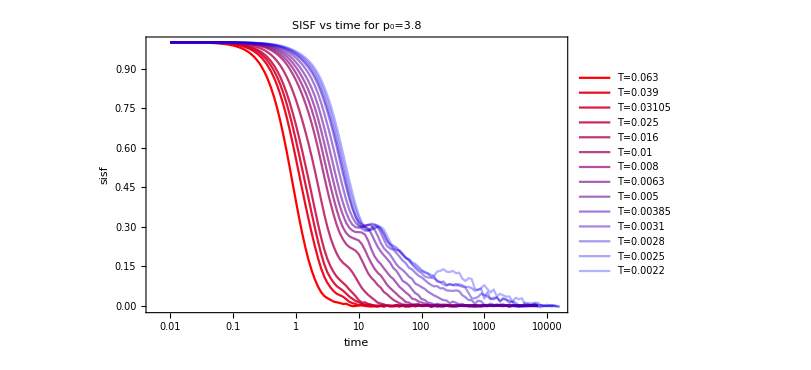
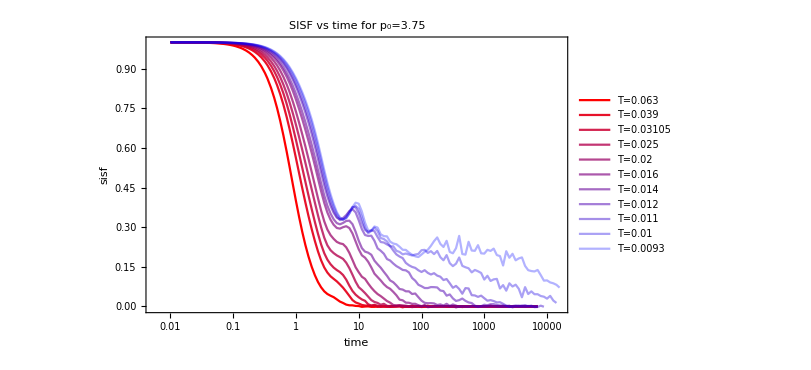

```mathematica
sisfPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],sisfMean[[p,T,rec]]},{rec,Length[sisfMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","sisf"},ImageSize->600,PlotLabel->"SISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}];
Column[sisfPlots]
```

```mathematica
fitCROverlapStartPos={46,47,49,50,54,58,60,62,64,67,69,75,75,75,75,75}
```

{46,47,49,50,54,58,60,62,64,67,69,75,75,75,75,75}

```mathematica
fitsCROverlap=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRoverlapMean[[T,rec]]]},{rec,fitOverlapStartPos[[T]],Length[overlapMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,0.99>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsCROverlap
```

{FittedModel[0.989954 ⅇ^(-0.405764 t^0.540588)],FittedModel[0.989987 ⅇ^(-0.219979 t^0.610297)],FittedModel[0.989991 ⅇ^(-0.166806 t^0.629919)],FittedModel[0.989993 ⅇ^(-0.120782 t^0.655342)],FittedModel[0.989996 ⅇ^(-0.0620973 t^0.697532)],FittedModel[0.989998 ⅇ^(-0.0254952 t^0.752693)],FittedModel[0.989998 ⅇ^(-0.0178276 t^0.751013)],FittedModel[0.989998 ⅇ^(-0.0116682 t^0.749091)],FittedModel[0.989999 ⅇ^(-0.00699925 t^0.75636)],FittedModel[0.989998 ⅇ^(-0.00399848 t^0.7572)],FittedModel[0.981051 ⅇ^(-0.00147709 t^0.792904)],FittedModel[0.989982 ⅇ^(-0.00132008 t^0.765856)],FittedModel[0.989848 ⅇ^(-0.000697377 t^0.798052)],FittedModel[0.976271 ⅇ^(-0.000211347 t^0.857844)],FittedModel[0.9672 ⅇ^(-0.00014312 t^0.861099)],FittedModel[0.964888 ⅇ^(-0.0000634493 t^0.887014)]}

```mathematica
tauCROverlapfits=Table[fitsCROverlap[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{5.30434,11.9547,17.1689,25.1649,53.7381,130.954,213.173,380.59,706.486,1469.16,3714.56,5750.6,9021.89,19230.9,29134.5,53982.2}

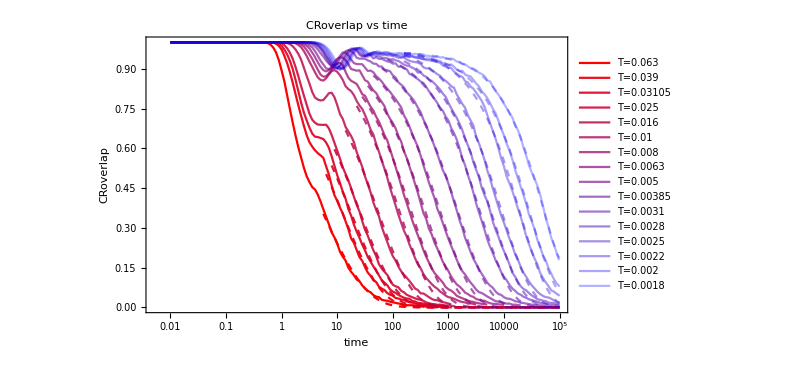

```mathematica
Show[CRoverlapPlot,Table[LogLinearPlot[fitsCROverlap[[T]][x],{x,time[[fitCROverlapStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

### overlap

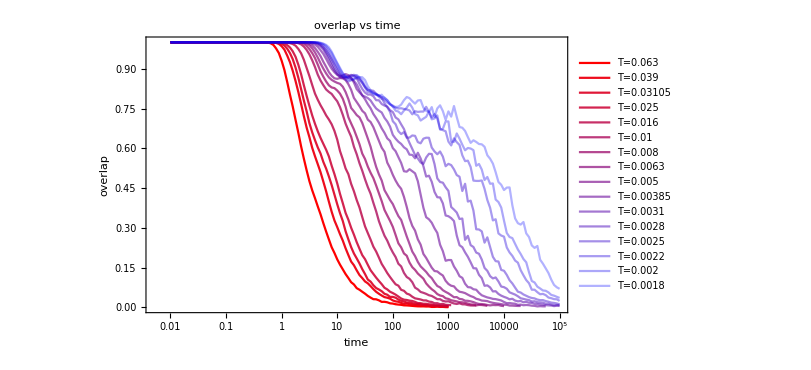

```mathematica
overlapPlot=ListLogLinearPlot[Table[Table[{time[[rec]],overlapMean[[T,rec]]},{rec,Length[CRoverlapMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs time",Joined->True]
```

```mathematica
fitOverlapStartPos={46,47,49,50,54,58,60,62,64,67,69,75,75,75,75,75}
```

{46,47,49,50,54,58,60,62,64,67,69,75,75,75,75,75}

```mathematica
fitsOverlap=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[overlapMean[[T,rec]]]},{rec,fitOverlapStartPos[[T]],Length[overlapMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,0.9>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsOverlap
```

{FittedModel[0.899949 ⅇ^(-0.416692 t^0.570721)],FittedModel[0.899984 ⅇ^(-0.257924 t^0.620357)],FittedModel[0.899988 ⅇ^(-0.18419 t^0.675023)],FittedModel[0.899991 ⅇ^(-0.158969 t^0.656324)],FittedModel[0.899992 ⅇ^(-0.0998525 t^0.67266)],FittedModel[0.899995 ⅇ^(-0.0642449 t^0.668794)],FittedModel[0.899995 ⅇ^(-0.0638978 t^0.608194)],FittedModel[0.899996 ⅇ^(-0.0488928 t^0.612934)],FittedModel[0.899998 ⅇ^(-0.0287827 t^0.652699)],FittedModel[0.899993 ⅇ^(-0.0263337 t^0.587713)],FittedModel[0.835829 ⅇ^(-0.0154975 t^0.586561)],FittedModel[0.860669 ⅇ^(-0.01795 t^0.537109)],FittedModel[0.733526 ⅇ^(-0.00228932 t^0.718824)],FittedModel[0.830126 ⅇ^(-0.00269093 t^0.656634)],FittedModel[0.784529 ⅇ^(-0.00107861 t^0.721048)],FittedModel[0.822266 ⅇ^(-0.00157456 t^0.642418)]}

```mathematica
tauOverlapfits=Table[fitsOverlap[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{4.63605,8.88505,12.259,16.4782,30.7319,60.6114,92.052,137.561,229.49,486.987,1217.13,1780.79,4710.57,8204.43,13032.7,23065.1}

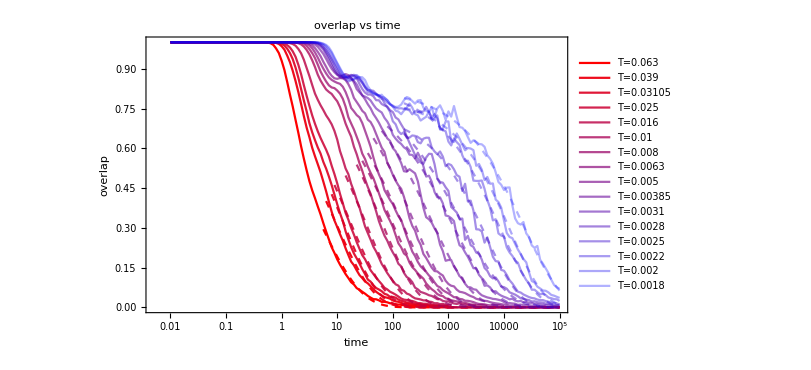

```mathematica
Show[overlapPlot,Table[LogLinearPlot[fitsOverlap[[T]][x],{x,time[[fitOverlapStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

#### CRSISF

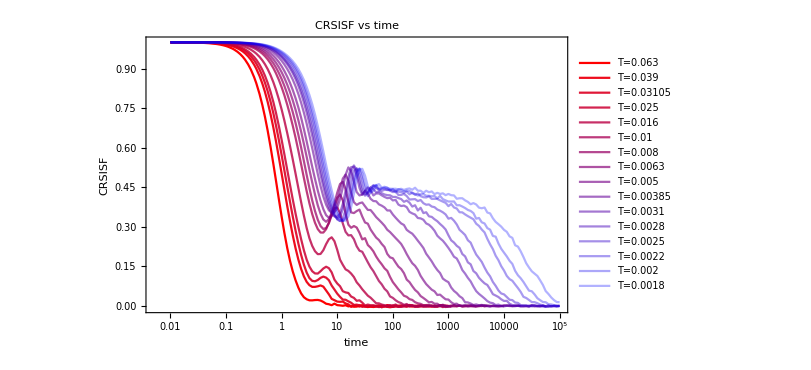

```mathematica
CRSISFPlot=ListLogLinearPlot[Table[Table[{time[[rec]],CRSISFMean[[T,rec]]},{rec,Length[CRSISFMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time",Joined->True]
```

```mathematica
fitCRSISFStartNum={5.223562384371017,5.9897781249014574,7.27896687589429,8.18350888496611,13.306468818755748,20.44545362547953,26.848904506044427,34.59556960139557,43.716132675532066,60.85859262176283,78.39053286118767,88.0976485665916,99.02222096719747,99.03378947388394,99.04535933208875,99.04535933208875};
```

```mathematica
fitCRSISFStartPos=Table[Position[time,_?(#>fitCRSISFStartNum[[i]]&)][[1,1]],{i,16}]
```

{46,47,49,50,54,58,60,62,64,67,69,70,71,71,71,71}

```mathematica
fitsCRSISF=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRSISFMean[[T,rec]]]},{rec,fitCRSISFStartPos[[T]],Length[CRSISFMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,0.5>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsCRSISF
```

{FittedModel[0.340381 ⅇ^(-1.00001 t^0.677533)],FittedModel[0.496301 ⅇ^(-0.456676 t^0.855332)],FittedModel[0.498335 ⅇ^(-0.294188 t^0.898438)],FittedModel[0.32385 ⅇ^(-0.173576 t^0.884069)],FittedModel[0.406731 ⅇ^(-0.0929931 t^0.899763)],FittedModel[0.464852 ⅇ^(-0.0420802 t^0.899866)],FittedModel[0.423376 ⅇ^(-0.0238347 t^0.899671)],FittedModel[0.446069 ⅇ^(-0.0208647 t^0.822498)],FittedModel[0.466417 ⅇ^(-0.0146888 t^0.787069)],FittedModel[0.453613 ⅇ^(-0.00644902 t^0.808849)],FittedModel[0.433253 ⅇ^(-0.00154885 t^0.884168)],FittedModel[0.449899 ⅇ^(-0.00207043 t^0.797151)],FittedModel[0.444015 ⅇ^(-0.000571504 t^0.899985)],FittedModel[0.444999 ⅇ^(-0.000278927 t^0.899993)],FittedModel[0.441695 ⅇ^(-0.000191544 t^0.89997)],FittedModel[0.445772 ⅇ^(-0.000115049 t^0.892181)]}

```mathematica
tauCRSISFfits=Table[fitsCRSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{0.999983,2.50014,3.9034,7.24834,14.011,33.8089,63.6444,110.477,213.261,510.714,1507.02,2327.63,4012.09,8901.97,13519.1,26010.6}

```mathematica
Length[TlistLongest]
```

0

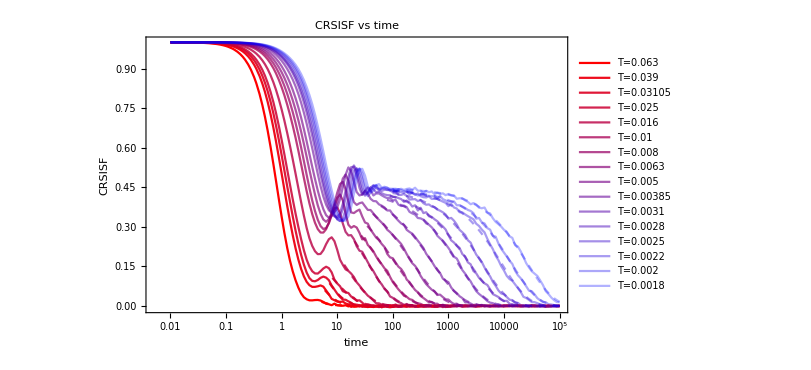

```mathematica
Show[CRSISFPlot,Table[LogLinearPlot[fitsCRSISF[[T]][x],{x,fitCRSISFStartNum[[T]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

#### SISF

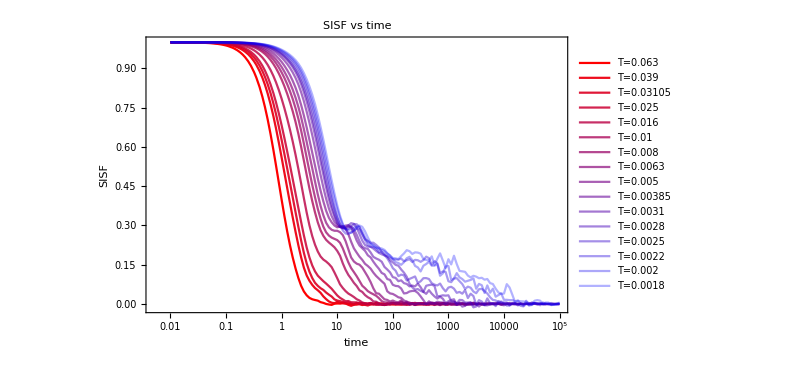

```mathematica
SISFPlot=ListLogLinearPlot[Table[Table[{time[[rec]],SISFMean[[T,rec]]},{rec,Length[SISFMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","SISF"},ImageSize->600,PlotLabel->"SISF vs time",Joined->True]
```

```mathematica
fitSISFStartPos={46,47,49,50,54,58,60,62,64,69,69,75,75,75,75,75}
```

{46,47,49,50,54,58,60,62,64,69,69,75,75,75,75,75}

```mathematica
fitsSISF=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[SISFMean[[T,rec]]]},{rec,fitSISFStartPos[[T]],Length[SISFMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,0.5>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsSISF
```

{FittedModel[0.389695 ⅇ^(-1.21686 t^0.84734)],FittedModel[0.471656 ⅇ^(-0.667003 t^0.87804)],FittedModel[0.475772 ⅇ^(-0.590409 t^0.769207)],FittedModel[0.492489 ⅇ^(-0.36901 t^0.862963)],FittedModel[0.401057 ⅇ^(-0.192664 t^0.896631)],FittedModel[0.496577 ⅇ^(-0.122052 t^0.897377)],FittedModel[0.294387 ⅇ^(-0.0722042 t^0.894352)],FittedModel[0.499604 ⅇ^(-0.06711 t^0.899403)],FittedModel[0.363914 ⅇ^(-0.0360303 t^0.898127)],FittedModel[0.192066 ⅇ^(-0.0290289 t^0.742003)],FittedModel[0.191781 ⅇ^(-0.0249584 t^0.680195)],FittedModel[0.146665 ⅇ^(-0.00995751 t^0.755348)],FittedModel[0.115751 ⅇ^(-0.00128434 t^0.899582)],FittedModel[0.210123 ⅇ^(-0.00352549 t^0.746696)],FittedModel[0.183986 ⅇ^(-0.00355128 t^0.688254)],FittedModel[0.219591 ⅇ^(-0.00369183 t^0.656228)]}

```mathematica
tauSISFfits=Table[fitsSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{0.793236,1.58599,1.98386,3.1748,6.27555,10.4212,18.8918,20.1574,40.4621,117.936,227.173,446.924,1637.08,1926.85,3623.88,5095.46}

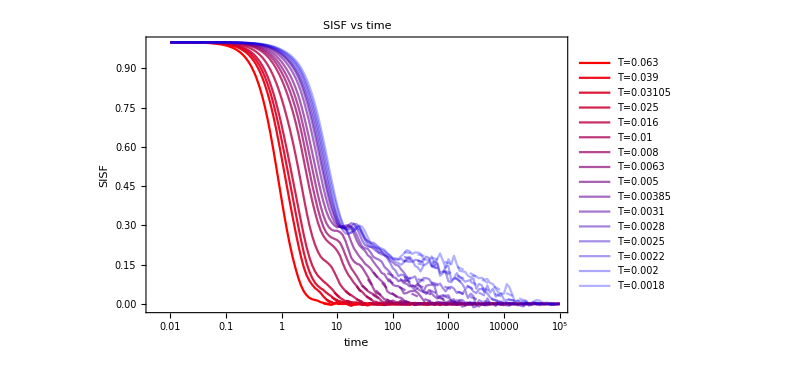

```mathematica
Show[SISFPlot,Table[LogLinearPlot[fitsSISF[[T]][x],{x,time[[fitSISFStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

#### Tau Alphas

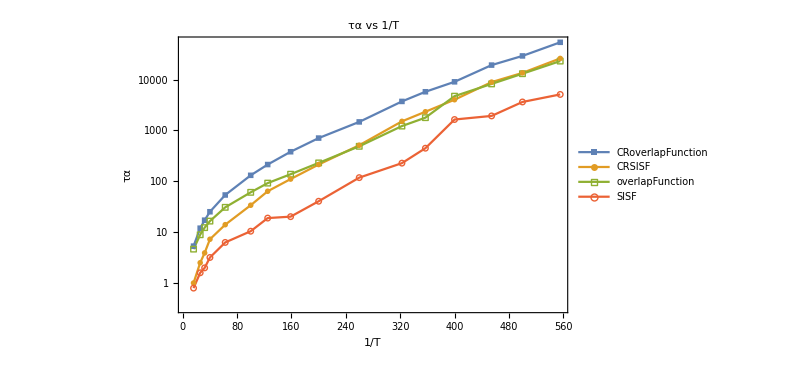

```mathematica
tauAlphafitingPlot=ListLogPlot[{Table[{1/Tlist[[T]],tauCROverlapfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauCRSISFfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauOverlapfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauSISFfits[[T]]},{T,Length[Tlist]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF","overlapFunction","SISF"},PlotMarkers->{Style["■",Large],Style["●",Large],Style["□",Large],Style["○",Large]},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
tauTable=Prepend[Table[{Tlist[[T]],tauCRSISFfits[[T]],tauCROverlapfits[[T]],tauOverlapfits[[T]],tauSISFfits[[T]]},{T,Length[Tlist]}],{"T","τα CRSISF","τα CR overlap","τα SISF","τα overlap"}]
```

{{T,τα CRSISF,τα CR overlap,τα SISF,τα overlap},{0.063,0.999983,5.30434,4.63605,0.793236},{0.039,2.50014,11.9547,8.88505,1.58599},{0.03105,3.9034,17.1689,12.259,1.98386},{0.025,7.24834,25.1649,16.4782,3.1748},{0.016,14.011,53.7381,30.7319,6.27555},{0.01,33.8089,130.954,60.6114,10.4212},{0.008,63.6444,213.173,92.052,18.8918},{0.0063,110.477,380.59,137.561,20.1574},{0.005,213.261,706.486,229.49,40.4621},{0.00385,510.714,1469.16,486.987,117.936},{0.0031,1507.02,3714.56,1217.13,227.173},{0.0028,2327.63,5750.6,1780.79,446.924},{0.0025,4012.09,9021.89,4710.57,1637.08},{0.0022,8901.97,19230.9,8204.43,1926.85},{0.002,13519.1,29134.5,13032.7,3623.88},{0.0018,26010.6,53982.2,23065.1,5095.46}}

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP380.csv",tauTable,"CSV"]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP380.csv

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha_p380.jpeg",tauAlphafitingPlot];
```

```mathematica
Export["/home/chengling/Research/updates/02012024/taualpha.jpeg",tauAlphafitingPlot,ImageResolution->600];
```

```mathematica
betaCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

{0.809979,0.796758,0.809037,0.809862,0.80979,0.809928,0.80995,0.809939,0.809968,0.80997,0.809986,0.809967,0.809928,0.703551,0.771414,0.809972,0.809195,0.809984,0.793789,0.809994,0.809994,0.809994,0.794059}

```mathematica
GCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

{0.449978,0.437055,0.448006,0.449785,0.449754,0.449922,0.449957,0.449934,0.449975,0.449977,0.44999,0.449993,0.441588,0.473171,0.454078,0.449017,0.44834,0.455473,0.448606,0.457386,0.45083,0.452285,0.449566}

```mathematica
betaCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

{0.529141,0.592079,0.569808,0.630995,0.641043,0.665991,0.691322,0.701875,0.704992,0.729689,0.738498,0.762204,0.759353,0.730815,0.74279,0.794476,0.764024,0.795187,0.765277,0.801778,0.865234,0.912167,0.836894}

```mathematica
GCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

{0.999912,0.999974,0.999974,0.999988,0.999992,0.999993,0.999996,0.999996,0.999997,0.999996,0.999997,0.999998,0.980185,0.993608,0.988459,0.976593,0.980814,0.978599,0.973606,0.976955,0.965694,0.961696,0.962681}

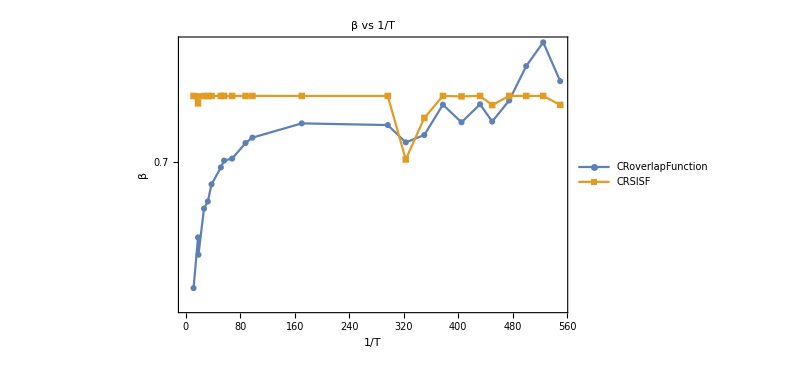

```mathematica
betafitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],betaCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],betaCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","β"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"β vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingBeta_p380_p380.jpeg",betafitingPlot,ImageResolution->600];
```

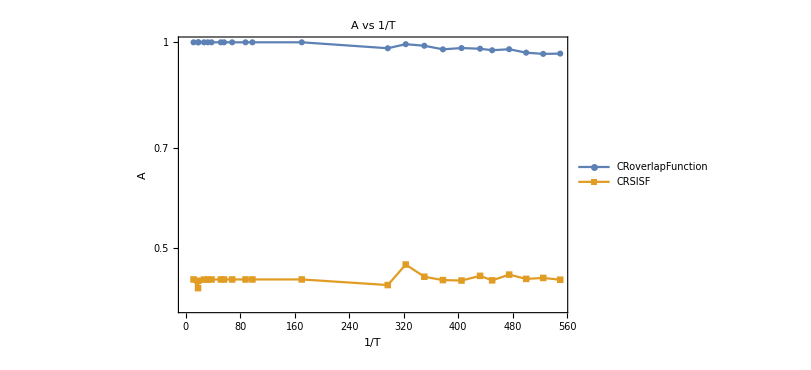

```mathematica
GfitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],GCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],GCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","A"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"A vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingA_p380_p380.jpeg",GfitingPlot,ImageResolution->600];
```

```mathematica
tauCRSISFAllT
```

{0.728537,1.41524,1.61389,2.6929,4.03698,5.21129,9.19522,9.51448,14.8936,25.9793,32.3344,138.256,1036.02,1239.22,2019.54,2804.8,4144.73,5262.53,6834.04,9346.07,13224.1,18754.3,19569.1}

```mathematica
tauTable=Prepend[Table[{TlistAllT[[T]],tauCRSISFAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],{"T","τα CRSISF","τα CR overlap"}]
```

{{T,τα CRSISF,τα CR overlap},{0.08868,0.728537,3.16039},{0.05586,1.41524,6.7635},{0.05409,1.61389,6.75448},{0.03756,2.6929,12.5106},{0.03105,4.03698,17.4891},{0.02652,5.21129,23.0389},{0.01945,9.19522,38.8819},{0.01782,9.51448,42.9591},{0.01471,14.8936,64.5399},{0.01141,25.9793,101.84},{0.01023,32.3344,125.531},{0.005873,138.256,436.846},{0.003371,1036.02,2732.95},{0.00309559,1239.22,3582.02},{0.00285428,2019.54,5140.15},{0.00264787,2804.8,7160.55},{0.00246931,4144.73,10064.4},{0.0023133,5262.53,13246.9},{0.00222222,6834.04,17008.4},{0.00210526,9346.07,22594.2},{0.002,13224.1,29109.1},{0.00190476,18754.3,39352.1},{0.00181818,19569.1,46020.2}}

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv",tauTable,"CSV"]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv

```mathematica
NumberForm[#,{9,6},ExponentFunction->(Null&)]&/@TlistAllT
```

{0.088680,0.055860,0.054090,0.037560,0.031050,0.026520,0.019450,0.017820,0.014710,0.011410,0.010230,0.005873,0.003371,0.003096,0.002854,0.002648,0.002469,0.002313,0.002222,0.002105,0.002000,0.001905,0.001818}

```mathematica
TlistAllT
```

{0.08868,0.05586,0.05409,0.03756,0.03105,0.02652,0.01945,0.01782,0.01471,0.01141,0.01023,0.005873,0.003371,0.00309559,0.00285428,0.00264787,0.00246931,0.0023133,0.00222222,0.00210526,0.002,0.00190476,0.00181818}

```mathematica
TlistGeneral={0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.28,0.0025,0.0022,0.002,0.0018}
```

{0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.28,0.0025,0.0022,0.002,0.0018}

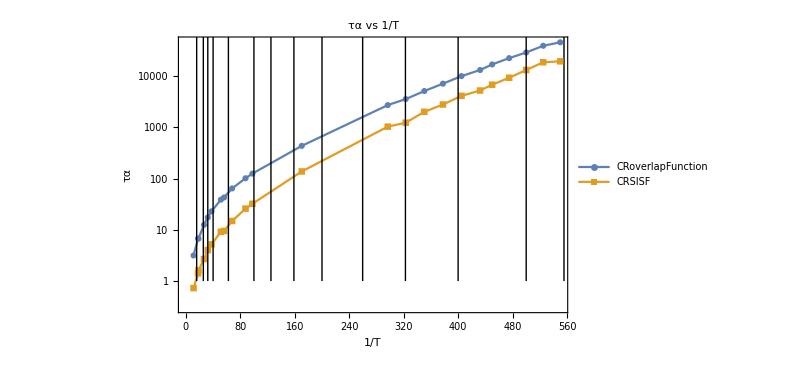

```mathematica
ListLogPlot[{Table[{1/TlistAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],tauCRSISFAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All,Epilog->Table[Line[{{1/TlistGeneral[[T]],0},{1/TlistGeneral[[T]],10000}}],{T,Length[TlistGeneral]}]]
```

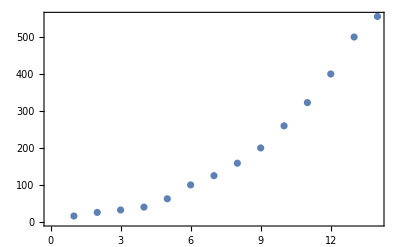

```mathematica
ListPlot[1/TlistGeneral]
```

```mathematica
tauEsGeneral={1.1841166706949628,2.462846296611076,3.8650575360708697,5.57413355409462,11.924841063370899,33.8105307104969,54.5761704083136,107.2953843344434,216.96587756816794,565.3189946945129,1243.945127271425,2065.,3731.3453237234366,7000.,12885.217184405017,22000.};
```

```mathematica
Length[TlistGeneral]
```

16